# Fractional Part

info@cafeplanck.com

```mathematica
FractionalPart[x]//TraditionalForm
```

frac(x)

```mathematica
PiecewiseExpand[FractionalPart[x],-3<x<3]
```

Piecewise[{{-2+x, x≥2}, {-1+x, 1≤x<2}, {x, -1<x<1}, {1+x, -2<x≤-1}, {2+x, True}}]

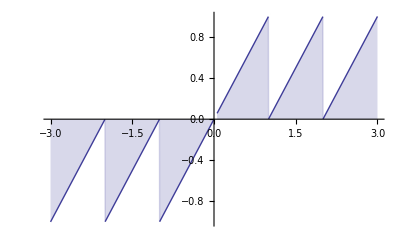

```mathematica
Plot[FractionalPart[x],{x,-3,3},Filling->Axis]
```